```mathematica
(*QuEST VQD Setup*)
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
```

URLDownload::invhttp: Failed writing body (0 != 16384).

```mathematica
CR[cq_,tq_,d_]:=Subscript[C, cq][Subscript[U, tq][{{1,0},{0,Exp[-2*Pi*I/2^(d+1)]}}]]
QFT[MaxQ_,MinQ_,Inv_]:=Module[{},Circ=Flatten[Table[CRS=Table[If[Nq-i>=MinQ,CR[Nq-i,Nq,i],{}],{i,MaxQ-MinQ,1,-1}];
 Flatten[Join[{Subscript[H, Nq]},CRS]],{Nq,MaxQ,MinQ,-1}]];
SWAPS=Table[If[MaxQ-i== MinQ+i,{},Subscript[SWAP, MaxQ-i,MinQ+i]],{i,0,Quotient[MaxQ-MinQ,2]}];
Circ=Flatten[Join[Circ,SWAPS]];
If [Inv==True,Reverse[Circ],Circ]]
```

```mathematica
{{1,0},{0,Exp[-2*Pi*I/2^(d+1)]}}//MatrixForm
```

(1 | 0
0 | ⅇ^(-ⅈ 2^-d π))

{SWAP_(2,0),H_0,C_1[U_0[{{1,0},{0,-ⅈ}}]],H_1,C_2[U_0[{{1,0},{0,-1}}]],C_2[U_1[{{1,0},{0,-ⅈ}}]],H_2}

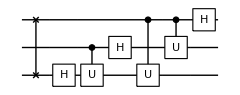

```mathematica
QFT[2,0,True]
DrawCircuit[%]
```

{H_0,H_1,H_2,Ph_0[(5 π)/4],Ph_1[(5 π)/2],Ph_2[5 π]}

{H_0,H_1,H_2,Ph_0[(5 π)/4],Ph_1[(5 π)/2],Ph_2[5 π],SWAP_(2,0),H_0,C_0[U_1[{{1,0},{0,-ⅈ}}]],H_1,C_1[U_2[{{1,0},{0,-ⅈ}}]],C_0[U_2[{{1,0},{0,ⅇ^(-(ⅈ π)/4)}}]],H_2}

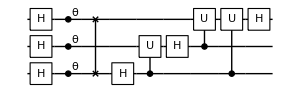

{7.55724×10^-33,2.03806×10^-33,7.55724×10^-33,1.49487×10^-32,4.36099×10^-32,1.,4.36099×10^-32,2.93115×10^-33}

```mathematica
DestroyAllQuregs[];
PrepTestState5={Subscript[H, 0], Subscript[H, 1], Subscript[H, 2], Subscript[Ph, 0][5*Pi/4], Subscript[Ph, 1][5*Pi/2], Subscript[Ph, 2][5*Pi]}
Psi=CreateQureg[3];
InitZeroState[Psi];
Circ2=Join[PrepTestState5,QFT[2,0,True]]
DrawCircuit[%]
ApplyCircuit[Psi,Circ2];
CalcProbOfAllOutcomes[Psi,{0,1,2}]
```

{C_3[Ph_0[π/4]],C_2[Ph_0[π/4]],C_2[Ph_0[π/4]],C_1[Ph_0[π/4]],C_1[Ph_0[π/4]],C_1[Ph_0[π/4]],C_1[Ph_0[π/4]]}

{H_3,H_1,H_2,X_0,C_3[Ph_0[π/4]],C_2[Ph_0[π/4]],C_2[Ph_0[π/4]],C_1[Ph_0[π/4]],C_1[Ph_0[π/4]],C_1[Ph_0[π/4]],C_1[Ph_0[π/4]],SWAP_(1,3),SWAP_(3,1),H_1,C_1[U_2[{{1,0},{0,-ⅈ}}]],H_2,C_2[U_3[{{1,0},{0,-ⅈ}}]],C_1[U_3[{{1,0},{0,ⅇ^(-(ⅈ π)/4)}}]],H_3}

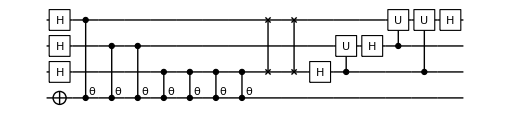

{}

{1.30963×10^-32,1.,1.30963×10^-32,3.08149×10^-33,7.70372×10^-34,6.16298×10^-33,7.70372×10^-34,3.08149×10^-33}

{{0},{0},{1}}

```mathematica
DestroyAllQuregs[];
Unitaries={Subscript[C, 3][Subscript[Ph, 0][Pi/4]],Subscript[C, 2][Subscript[Ph, 0][Pi/4]],Subscript[C, 2][Subscript[Ph, 0][Pi/4]],Subscript[C, 1][Subscript[Ph, 0][Pi/4]],Subscript[C, 1][Subscript[Ph, 0][Pi/4]],Subscript[C, 1][Subscript[Ph, 0][Pi/4]],Subscript[C, 1][Subscript[Ph, 0][Pi/4]]}
PhEstCirc=Join[{Subscript[H, 3],Subscript[H, 1],Subscript[H, 2],Subscript[X, 0]},Unitaries,{Subscript[SWAP, 1,3]},QFT[3,1,True](*,{Subscript[M, 0],Subscript[M, 1],Subscript[M, 2]}*)]
DrawCircuit[%]
ψ=CreateQureg[4];
InitZeroState[ψ];
ApplyCircuit[ψ,PhEstCirc]
CalcProbOfAllOutcomes[ψ,{1,2,3}]
ApplyCircuit[ψ,{Subscript[M, 3],Subscript[M, 2],Subscript[M, 1]}]
```